# Homework 3

Wang Long 1101110160

## Question 1

For an NFW halo, please analyze if there exists a phase-space distribution function that depends only on the energy E. If yes, please calculate f(E) for the cases with cvir = 4,10, 20, respectively, and show the results in Figure 1.

Abel integral 
	f(ϵ)=1/(√8 π^2) d/dϵ∫_0^ϵ dρ/dΨ  ⅆΨ/(√(ϵ-Ψ))

### Code

```mathematica
Get["/Users/wanglong/Dropbox/Writing/lessons/dynamics/Homework3dat"];
```

```mathematica
(*rs=0.1;δ0=1;ρc=1;G=1;
q1ρ[r_]=(δ0 ρc)/((r/rs)(1+r/rs)^2);
q1M[r_]=4π ρc rs^3(Log[1+r/rs]-(r/rs)/(1+r/rs));
(*q1Φ[r_]=-G Integrate[ q1M[Rr]/Rr^2,{Rr,r,∞},Assumptions->{rs>0,r>0}]*)
q1Φ[r_]=-4π G ρc rs^2 Log[1+r/rs]/(r/rs);
q1Ψ[r_]=-q1Φ[r];*)
q1v=110;q1rv=2;q1G=1;
q1ρc=1/(4/3 π q1rv^3 q1v);
q1g[c_]:=1/(Log[1+c]-c/(1+c));
q1M[r_,c_]=q1g[c]*(Log[1+c r]-(c r)/(1+c r));
q1ρ[r_,c_]=(q1v c^2 q1g[c]q1ρc)/(3r(1+c r)^2);
q1Ψ[r_,c_]=q1g[c] Log[1+c r]/r 4/3 π q1G q1rv^2 q1v q1ρc;
```

```mathematica
Off[NSolve::ifun]
Off[NIntegrate::ncvb]
(*q1dρ2dΨ2[r_]=Simplify[D[Simplify[D[q1ρ[r],r]/D[q1Ψ[r],r]],r]/D[q1Ψ[r],r]];
q1dΨ[r_]=Simplify[D[q1Ψ[r],r]];
q1r[ϵ_]:=r/.NSolve[q1Ψ[r]==ϵ,r][[1,1]]
q1f[ϵ_,rl_]:=1/(√8 π^2)NIntegrate[q1dρ2dΨ2[r]/(√(ϵ-q1Ψ[r]))*q1dΨ[r],{r,∞,rl}]*)
q1dρ2dΨ2[r_,c_]=Simplify[D[Simplify[D[q1ρ[r,c],r]/D[q1Ψ[r,c],r]],r]/D[q1Ψ[r,c],r]];
q1dΨ[r_,c_]=Simplify[D[q1Ψ[r,c],r]];
q1r[ϵ_,c_]:=r/.NSolve[q1Ψ[r,c]==ϵ,r][[1,1]]
q1f[ϵ_,c_]:=1/(√8 π^2)NIntegrate[q1dρ2dΨ2[r,c]/(√(ϵ-q1Ψ[r,c]))*q1dΨ[r,c],{r,∞,q1r[ϵ,c]+0.0001}]
q1plot:=ListPlot[Table[{e,Log10[q1f[-e,i]]},{i,{4,10,20}},{e,-2.5,-0.0001,0.05}],PlotRange->{{-2.5,-0},{-6,3}},AxesLabel->{"E","Log[f]"},AxesOrigin->{-2.5,-6},Joined->True,AspectRatio->1]
(*q1plot:=Plot[Table[Log10[q1f[-e,i]],{i,{4,10,20}}],{e,-2.5,-0.0001}]*)
```

### Discussion

### Figures & Tables

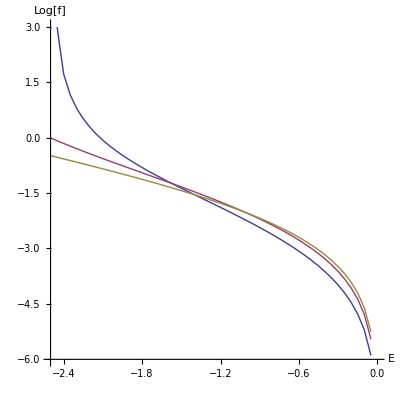

Figure 1: distribution function vs E

```mathematica
q1plot
"Figure 1: distribution function vs E"
```

## Question 2

In more general cases with anisotropic velocity dispersions indicated by   β=1− σ_θ^2/σ_r^2 the Jeans equation for the radial velocity dispersion can be written as 1/ρ d/dr(ρ σ_r^2)+2β σ_r^2/r=- dΦ/dr 
Please calculate σr2(r) for β = 0 and cvir=4, 10, 20, respectively and plot the results in Figure 2. Calculate also the cases with
c_vir=10, but β = 0, 0.5,1, respectively, and show the results in Figure 3.

### Code

```mathematica
Do[q2σr2[i][j][r_]=σr2[r]/.(DSolve[{1/q1ρ[r,c] D[q1ρ[r,c]*σr2[r],r]+2β σr2[r]/r==q1dΨ[r,c],σr2[1*^11]==0},σr2[r],r]/.{c->i,β->j/2.})[[1,1]];
,{i,{4,10,20}},{j,{0,1,2}}]
```

```mathematica
q2color={Red,Blue,Green};
q2index={4,10,20};
q2plotb:=Show[Table[Plot[Sqrt[q2σr2[10][j][10^r]/(4/3π q1rv^2 q1v q1ρc)],{r,-2,1},PlotStyle->q2color[[j+1]]],{j,{0,1,2}}],AxesOrigin->{-2,0},PlotRange->{{-2,1},{0,3}},AxesLabel->{"Log[r/r_s]","σ_r/V_V"}]
q2plotc:=Show[Table[Plot[Sqrt[q2σr2[q2index[[i]]][0][10^r]/(4/3π q1rv^2 q1v q1ρc)],{r,-2,1},PlotStyle->q2color[[i]]],{i,3}],AxesOrigin->{-2,0},PlotRange->{{-2,1},{0,1.5}},AxesLabel->{"Log[r/r_s]","σ_r/V_V"}]
```

### Plot

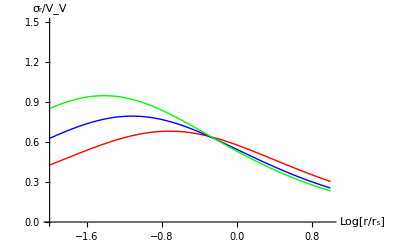

Figure 2: Red: c=4; Blue: c=10; Green: c=20

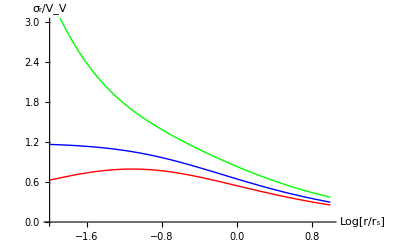

Figure 3: Red: β=0; Blue: β=0.5; Green: β=1

```mathematica
q2plotc
"Figure 2: Red: c=4; Blue: c=10; Green: c=20"
q2plotb
"Figure 3: Red: β=0; Blue: β=0.5; Green: β=1"
```

## Question 3:

For the two sets of parameters considered in (2), please calculate the potential energy W(r) and the kinetic energy T(r), respectively for each case, and show the results of 2T/W in Figure 4 (β=0 and cvir=4,10,20) and Figure 5 (cvir=10, but β=0,0.5,1).
Have the considered halos reached virial equilibrium yet?

### Code

```mathematica
q3W[s_,c_]:=(- 1)/q1rv NIntegrate[q1M[r,c]/r*D[q1M[r,c],r],{r,0,s}]
q3T[s_,c_,b_]:=2π q1rv^3 NIntegrate[(3-b)q1ρ[r,c]q2σr2[c][b][r] r^2,{r,0,s}]
q3clist=Table[{r,2q3T[10^r,c,0]/Abs[q3W[10^r,c]]},{c,{4,10,20}},{r,-2,1,0.1}];
q3blist=Table[{10^r,2q3T[10^r,10,b]/Abs[q3W[10^r,10]]},{b,0,2,1},{r,-2,1,0.1}];
```

```mathematica
q3plotc:=ListPlot[q3clist,Joined->True,PlotStyle->{Red,Blue,Green},AxesOrigin->{-2,0},AxesLabel->{"log[r/r_s]","2T/|W|"}]
q3plotb:=ListLogLogPlot[q3blist,Joined->True,PlotStyle->{Red,Blue,Green},AxesOrigin->{0.01,1},AxesLabel->{"log[r/r_s]","2T/|W|"}]
```

```mathematica
Save["/Users/wanglong/Dropbox/Writing/lessons/dynamics/Homework3dat","`*"]
```

### Plot

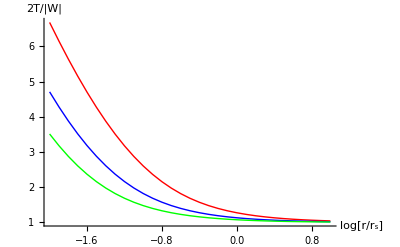

Figure 4: Red: c=4; Blue: c=10; Green: c=20

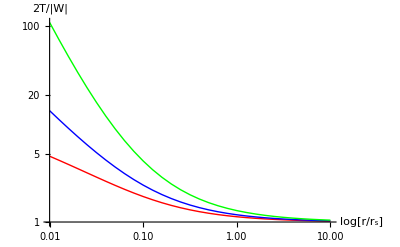

Figure 5: Red: β=0; Blue: β=0.5; Green: β=1

```mathematica
q3plotc
"Figure 4: Red: c=4; Blue: c=10; Green: c=20"
q3plotb
"Figure 5: Red: β=0; Blue: β=0.5; Green: β=1"
```

### Discussion

The Q value is much larger than 1 at small radius and close to 1 at r=rs, so the system does not exactly reach virial equilibrium. For larger concentration system, it’s closer to virial equilibrium comparing with smaller concentration system. In addition, isotropic velocity dispersion system is closer to virial equilibrium than anisotropic system.